```mathematica
genSound[ music_]:=(
soundNoteList[list_]:= Apply[SoundNote, list];
generated = Map[soundNoteList, music];
sound = Sound[generated];
Return[sound];
)
```

```mathematica
(* Přečtěte si dokumentaci na https://reference.wolfram.com/language/ref/SoundNote.html *)
```

```mathematica
music = {{{0,-10}, "Piano"}}
genSound[music]
```

{{{0,-10},Piano}}

Sound[{SoundNote[{0,-10},Piano]}]

```mathematica
genSound[{{{0,4}, "Harpsichord"}}]
```

Sound[{SoundNote[{0,4},Harpsichord]}]

```mathematica
{{genSound[{{2, "Harpsichord"}}]}, {□}}
```

{{Sound[{SoundNote[2,Harpsichord]}]},{□}}

```mathematica
{{Sound}, {□}}[{SoundNote[{0,4},{0,2},"Hapsichord"]}]
```

{{Sound},{□}}[{SoundNote[{0,4},{0,2},Hapsichord]}]

```mathematica
{{genSound[{{2, "Harpsichord"}}]}, {□}}
```

{{Sound[{SoundNote[2,Harpsichord]}]},{□}}

{{{0,4},{0,0.5},Harpsichord},{2,{0.5,1.5},Piano},{-1,2,Flute},{0,1,Flute}}

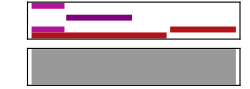

-Graphics-

```mathematica
music = {{{0,4}, {0,0.5}, "Harpsichord"},{2, {0.5,1.5}, "Piano"}, {-1, 2, "Flute" }, {0,1,"Flute"}}
genSound[music]
```

```mathematica
music = {{{0,4}, "Harpsichord"}}
genSound[music]
```

{{{0,4},Harpsichord}}

Sound[{SoundNote[{0,4},Harpsichord]}]

```mathematica
NormalDistribution[0,1]
```

NormalDistribution[0,1]

```mathematica
RandomVariate[NormalDistribution[0.5, 0.5]]
```

0.679453

```mathematica
GetMelody[size_] := (
melody = {0};
For[i=1, i<size,i++, (
previous = Part[melody, i];
next =Round[RandomVariate[NormalDistribution[0, 2]]] + previous; 
AppendTo[melody, next];
)];
Return[melody];
)
```

```mathematica
CreateMusic[melody_, tones_, rythm_] := (
music = {};
For[i=0, i<Length[melody],i++, (
toneOffset = Part[melody, i+1];
tone = Part[tones, 1 + Mod[toneOffset, Length[tones]]] + (Floor[toneOffset / Length[tones]] * 12);
sound = {tone, Part[rythm, i + 1] * 1.5, "ElectricGuitar"};
AppendTo[music,sound];
)];
Return[music];
)
```

```mathematica
GetRythm[divCoef_, recursionCoef_] := (
If[RandomReal[] > divCoef,(
Return[{1}]
),(
divLen[e_] := e / 2;
Return[ Map[divLen, Join[GetRythm[divCoef / recursionCoef, recursionCoef], GetRythm[divCoef/recursionCoef, recursionCoef]]]];
)]
)
```

{1/4,1/4,1/4,1/4,1/2,1/2,1/2,1/2}

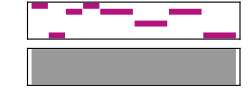

```mathematica
rtm = Join[GetRythm[2, 4], GetRythm[1, 2], GetRythm[1, 2]]
genSound[CreateMusic[GetMelody[Length[rtm]], {0, 2, 4, 5, 7, 9, 11}, rtm]]
```

```mathematica
RandomReal[]
```

0.480992

```mathematica
NumberForm[0.7611540449832752,100]
```

0.7611540449832752

{1/2,{1/4,{1/4}}}

{1/2,{1/4,{1/4}}}

{1/2,{1/4,{1/4}}}

«9 more identical outputs»

{1/4,{1/4},{1/2}}

{1/2,{1/4,{1/4}}}

{1/4,{1/4},{1/2}}

GetRythm[1,2]

GetRythm[1,2]

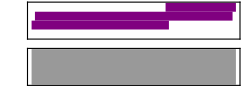

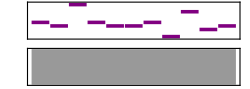
6 -Graphics-

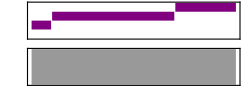

```mathematica
{1/2,{1/4,{1/4}}}
```